# On a three-dimensional tumor-virus compartmental model

This Mathematica Notebook is a supplementary material to the paper“On a three-dimensional and two four-dimensional
oncolytic viro-therapy models”. It contains some of the calculations and illustrations appearing in the paper.

#### 1) Section 2 (in paper): Deterministic model with Logistic growth [Tian2011]

### 0) Definition of the model [Tian11]:

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
(*Some aliases*)
Format[βv]:=Subscript[β,v];Format[βy]:=Subscript[β,y];
(****** Four dim Deterministic  epidemic model with Logistic growth ****)
x1=λ  x(1-(x+y)/K)-   β x v ;
y1=β x v -βy y z- γ y;
v1=-β x v - βv  v z+ b  γ y - δ v;

par={λ,δ,β,b};X={x,y,v};
val={0.36,0.44,0.11,28};
parN=Thread[par->val];
par2=Thread[{λ,δ}->{0.36,0.44}];
cp={λ>0,δ>0,β>0,b>1};
c3dim={βv->0,βy->0,γ->1, K->1};
cnTian={λ->0.36,β->0.11,δ->0.44,K->1,γ->1,βv->0, βy->0}(*Numerical values of Tian*);

dyn={x1,y1,v1}/.βy->0/.βv->0(*Tian 11 case with K>0*);
dynKeq1=dyn/.c3dim;
Print[" (x'
y'
v')=",dyn//FullSimplify//MatrixForm, 
"and the reparametrized dynamics [Tian 2011] are  (x'
y'
v')=",
dynKeq1//FullSimplify//MatrixForm]

R0=b β K/(β K+δ);b0=1+δ/(β K);
Print["R0=", R0, " , b0=", b0]
```

(x'
y'
v')=(-v x β+x (1-(x+y)/K) λ
v x β-y γ
b y γ-v (x β+δ))and the reparametrized dynamics [Tian 2011] are  (x'
y'
v')=(-x (v β+(-1+x+y) λ)
-y+v x β
b y-v (x β+δ))

R0=(b K β)/(K β+δ) , b0=1+δ/(K β)

Fixed points and analysis of the Stability via Routh Hurwitz:

```mathematica
cfp=Solve[Thread[dyn=={0,0,0}],{x,y,v}]//FullSimplify;
fp=X/.cfp;

Print["Number of fixed points is ",Length[fp]," The third FP is E*="]
fp[[3]]//FullSimplify
fpN=fp/.c3dim/.parN;
Print["in first fig. E*=",fpN[[3]]]
(*"Jacobian is"*)
Jac=Grad[dyn,{x,y,v}]//FullSimplify;
J0=Jac/.cfp[[1]];J0//MatrixForm;
Print["J(E_K) and its det are"]
J1=Jac/.cfp[[2]];J1//MatrixForm
Det[J1]//Factor
Print["J(E_*) "]
Jst=Jac/.cfp[[3]]//FullSimplify;Jst//MatrixForm
(*Jstcr=Jst/.b->b0//FullSimplify;*)

(*Routh Hurwitz conditions for the stability of E_***)
pc=Collect[Det[ψ IdentityMatrix[3]-Jst],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Print["a_1=",a1=Apart[coT[[3]]]//.c3dim, ", a_2=",a2=coT[[2]]//.c3dim, ", a_3=",a3=coT[[1]]//.c3dim]
H2=a1*a2-a3;
Print["Hurw(b) when K=γ=1 is H2=", H2//.c3dim//FullSimplify]
Print["H2(b0) when K=γ=1 is",H2/.b->b0//.c3dim//FullSimplify]
Print["Denominator of H2 is posi",Denominator[Together[H2]]/.K->1//FullSimplify]
Together[H2//FullSimplify];
ϕb=Collect[Numerator[Together[H2]]/(δ λ),b]/.K->1//FullSimplify;
(*Print["ϕ(b)=", Collect[ϕb,b]]*)
Print["value of ϕ(b) at crit b is posi "]
ϕb/.b->b0/.K->1//FullSimplify
cofi=CoefficientList[ϕb,b]//FullSimplify;
Print["Coefficients of numerator ϕ(b)are {B0,B1,B2,B3,B4}=",cofi]
(*ϕb/.b->1//FullSimplify*)
Print[" shifted coefs: "]
ϕbsh=Collect[ϕb/.b->(b0/.K->1)+b,b];
cofi=CoefficientList[ϕbsh,b]//FullSimplify
Print["There is no solution of B2<0 AND B3>0 for shifted pol: "]

eq=Join[{cofi[[4]]>0&&cofi[[3]]<0},cp];
Reduce[eq,λ]
FindInstance[Join[{cofi[[4]]>0&&cofi[[3]]<0},cp],par]
(*;
Reduce[Join[{cofi[[4]]>0&&cofi[[3]]<0},cp],par]//FullSimplify;*)
Print["There are solutions for BOTH B2<0 AND B3>0, separately: "]
eq=Join[{cofi[[4]]>0},cp];
Reduce[eq,λ]
eq=Join[{cofi[[3]]<0},cp];
Reduce[eq,λ]
```

Number of fixed points is 3 The third FP is E*=

{δ/((-1+b) β),(((-1+b) K β-δ) δ λ)/((-1+b) β ((-1+b) K β γ+δ λ)),(γ ((-1+b) K β-δ) λ)/(β ((-1+b) K β γ+δ λ))}

in first fig. E*={0.148148,0.0431317,2.64672}

J(E_K) and its det are

(-λ | -λ | -K β
0 | -γ | K β
0 | b γ | -K β-δ)

γ (-K β+b K β-δ) λ

J(E_*)

((δ λ)/(K β-b K β) | (δ λ)/(K β-b K β) | -δ/(-1+b)
(γ ((-1+b) K β-δ) λ)/((-1+b) K β γ+δ λ) | -γ | δ/(-1+b)
(γ (K (β-b β)+δ) λ)/((-1+b) K β γ+δ λ) | b γ | (b δ)/(1-b))

a_1=(-1+b+b δ)/(-1+b)+(δ λ)/((-1+b) β), a_2=(δ λ ((-1+b) β (-1+b+β-b β+δ+b δ)+((-1+b)^2 β+b δ^2) λ))/((-1+b)^2 β ((-1+b) β+δ λ)), a_3=δ (1+δ/(β-b β)) λ

Hurw(b) when K=γ=1 is H2=δ λ (-1+δ/((-1+b) β)-((β (-1+b+b δ)+δ λ) ((-1+b)^2 β^2-b δ^2 λ-(-1+b) β (-1+δ-λ+b (1+δ+λ))))/((-1+b)^3 β^2 ((-1+b) β+δ λ)))

H2(b0) when K=γ=1 is(1+β+δ) λ (1+β+δ+λ)

Denominator of H2 is posi(-1+b)^3 β^2 ((-1+b) β+δ λ)

value of ϕ(b) at crit b is posi

(δ^3 (1+β+δ) (1+λ) (1+β+δ+λ))/β

Coefficients of numerator ϕ(b)are {B0,B1,B2,B3,B4}={β (1+λ) (-β+δ λ),-β^3 (-1+δ)+δ^3 λ^2-β δ λ (2+3 δ+2 λ)+β^2 (3+3 δ-δ^2+3 λ),β (β^2 (-3+2 δ)-3 β (1+2 δ+λ)+δ λ (1+δ (3+δ)+λ)),β^2 (1-β (-3+δ)+δ (3+δ)+λ),-β^3}

shifted coefs:

{(δ^3 (1+β+δ) (1+λ) (1+β+δ+λ))/β,δ^2 (3+δ (5+3 δ)+5 λ+2 δ (3+δ) λ+(2+δ) λ^2+β (3+3 δ+3 λ+2 δ λ)),β δ (3-β^2+3 δ (1+δ)+4 λ+δ (3+δ) λ+λ^2),β^2 (1+(-1+δ) δ-β (1+δ)+λ),-β^3}

There is no solution of B2<0 AND B3>0 for shifted pol:

False

{}

There are solutions for BOTH B2<0 AND B3>0, separately:

(δ>0&&0<β≤(1-δ+δ^2)/(1+δ)&&b>1&&λ>0)||(δ>0&&β>(1-δ+δ^2)/(1+δ)&&b>1&&λ>-1+β+δ+β δ-δ^2)

δ>0&&β>√(3+3 δ+3 δ^2)&&b>1&&0<λ<1/2 (-4-3 δ-δ^2)+1/2 √(4+4 β^2+12 δ+5 δ^2+6 δ^3+δ^4)

Bifurcation diagram of codimension 2:

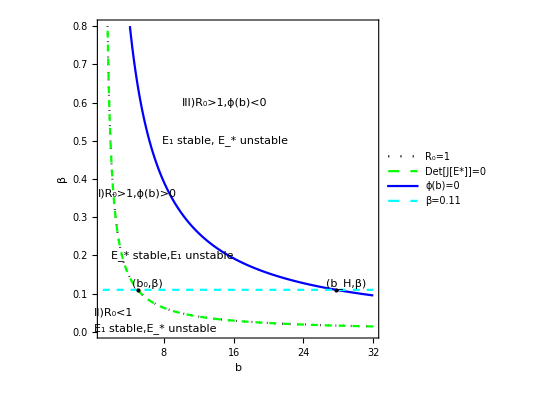

map3.pdf

```mathematica
bm=1; bM=32; ym=0; yM=0.8;
R01=R0/.c3dim/.par2;
a3N=a3/.par2;
a1N=a1/.par2;
phiN=ϕb/.par2//FullSimplify;

pt1s=Text["(b_0,β)",Offset[{10,6},{b0/.c3dim/.par2/.β->0.11,0.11}]];
pt1={PointSize[Medium],Style[Point[{b0/.c3dim/.par2/.β->0.11,0.11}],Black]};
ptHs=Text["(b_H,β)",Offset[{10,6},{27.7664,0.11}]];
ptH1={PointSize[Medium],Style[Point[{27.7664,0.11}],Black]};
R1=Style[Text["I)R_0>1,ϕ(b)>0",{5,0.36}],10];R1a=Style[Text["E_* stable,E_1 unstable",{9,0.2}],10];
R2=Style[Text["II)R_0<1",{2.2,0.05}],11];R2a=Style[Text["E_1 stable,E_* unstable",{7,0.01}],11];
R3=Style[Text["III)R_0>1,ϕ(b)<0",{15,0.6}],13];R3a=Style[Text["E_1 stable, E_* unstable ",{15,0.5}],13];
epi={pt1,pt1s,ptHs,ptH1,R1,R1a,R2,R2a,R3,R3a};

pR0=ContourPlot[R01==1,{b,bm,bM},{β,ym,yM},ContourStyle->{Black,Dotted},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"R_0=1"}];
pphi1=ContourPlot[phiN==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Blue,Bold},PlotPoints -> 200,
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"ϕ(b)=0"}];
pa1=ContourPlot[a1N==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Red,Bold},
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"Tr[J[E*]]=0"}];
pa3=ContourPlot[a3N==0,{b,bm,bM},{β,ym,yM},ContourStyle->{Green,Dashed},PlotPoints -> 180,
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"Det[J[E*]]=0"}];
pbeta=ContourPlot[β==0.11,{b,bm,bM},{β,ym,yM},ContourStyle->{Cyan,Dashed},PlotPoints -> 180,
 FrameLabel->{"b","β"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"β=0.11"}];
 
 peq={pR0,pa3,(*pa1,*)pphi1,pbeta};
pcut=Show[peq,Epilog->epi]
Export["map3.pdf",pcut]
```

3D parametric plot:

```mathematica
Xt=Map[#[t]&,X ];
ct=Thread[X->Xt];
dynt=dynKeq1/.ct;
x1=dynt[[1]] ;
y1=dynt[[2]];
v1=dynt[[3]];
X0={0.4,0.05,0.05};
ode={x'[t]==x1,y'[t]==y1,v'[t]==v1,x[0]==X0[[1]],y[0]==X0[[2]],v[0]==X0[[3]]};
T=2800;
odeN=ode/.parN
solr=NDSolve[odeN,{x,y,v},{t,0,T}];

cyR=ParametricPlot3D[{  x[t],y[t],v[t]}/.solr,{t,0,T}, BoxRatios->{1,1,1},AxesLabel->{"x","y","v"},
PlotRange->Full,PlotStyle->{Red,Dashed}];
pt0={PointSize@.02, Style[Point[X0],Black]};pt0s=Text[Style["(x_0,y_0,v_0)", 10], X0];
pts={PointSize@.02, Style[Point[fpN[[3]]],Black]}; ptss=Text[Style["(x_*,y_*,v_*)", 10] ,fpN[[3]] 
];
pts={ptss,pt0,pt0s,pts};
```

{x'[t]==-0.11 v[t] x[t]+0.36 x[t] (1-x[t]-y[t]),y'[t]==0.11 v[t] x[t]-y[t],v'[t]==-0.44 v[t]-0.11 v[t] x[t]+28 y[t],x[0]==0.4,y[0]==0.05,v[0]==0.05}

```mathematica
cyR3=Show[{cyR}, Graphics3D[pts], Axes -> True,
 BoxRatios -> 1]
```

-Graphics3D-

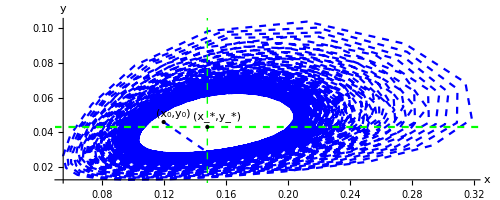

T11R.pdf

T11B.pdf

```mathematica
(****************b=28; different initial values   ******************)
b=28;T1=4000;
x0n=0.12; y0n=0.046;v0n=0.01;
ode={x'[t]==x1,y'[t]==y1,v'[t]==v1,x[0]==x0n,y[0]==y0n,v[0]==v0n};
sol=NDSolve[ode/.cnTian,{x,y,v},{t,0,T1}];
(*****¨Parametric plot conditions***)

cyB=ParametricPlot[{  x[t],(y[t])}/.sol,{t,0,T1}, AxesLabel->{"x","y"},
PlotRange->Full,PlotStyle->{Dashed,Blue}];
pyn=Plot[(fp[[3,2]]/.cnTian),{t,0,T1},PlotStyle->{Dashed,Green}];
cyBall=Show[{cyB,pyn, Graphics[{Green,Dashed,
Line[{{fp[[3,1]]/.cnTian,0},{fp[[3,1]]/.cnTian,1}}]}] },
Epilog->{{Text["(x_*,y_*)",Offset[{10,10},{(fp[[3,1]]/.cnTian),(fp[[3,2]]/.cnTian)}]],
{PointSize[Large],Style[Point[{(fp[[3,1]]/.cnTian),(fp[[3,2]]/.cnTian)}],Black]}},
{PointSize[Large],Point[{x0n,y0n}]},Text["(x_0,y_0)",Offset[{10,8},{x0n,y0n}]]}]


cyr=ParametricPlot[{  x[t],(y[t])}/.solr,{t,0,T}, AxesLabel->{"x","y"},PlotStyle->{Red}];
cyRall=Show[{cyr},PlotRange->{{0.05,0.35},{0,0.12}},Epilog->
{{PointSize[Large],Point[{X0[[1]],X0[[2]]}]},Text["(x_0,y_0)",Offset[{10,8},{X0[[1]],X0[[2]]}]]}];

Export["T11R.pdf",cyr]
Export["T11B.pdf",cyB]
```

Computations of the Jacobians and Eigenvalues using EcoEvo package:

```mathematica
<<EcoEvo`
(*EcoEvoDocs;*)
(********Analysis of the Model, K=γ=1; must redefine fp, cp***)
ClearParameters;Clear["b"];
SetModel[{Pop[x]->{Equation:>dynKeq1[[1]],Color->Red},Pop[y]->
{Equation:>(dynKeq1[[2]]),Color->Green},
Pop[v]->{Equation:>(dynKeq1[[3]]),Color->Purple},
 Parameters:>(cp)}]

fpT=SolveEcoEq[]//FullSimplify

J0T=EcoJacobian[fpT[[1]]]//FullSimplify;
J1T=EcoJacobian[fpT[[2]]]//FullSimplify;
Jst=EcoJacobian[fpT[[3]]]//FullSimplify;
Print["Jac(E_0)=",J0T//MatrixForm]
Print["Jac(E_1)=",J1T//MatrixForm]
Print["Jac(E_*)=",Jst//MatrixForm]
Print["Eigenvalues of E_1 are:",eiT=EcoEigenvalues[fpT[[2]]]//FullSimplify]

Print["b_0=b_s1=",bs1=Apart[Last[Last[Reduce[Join[{eiT[[2]]>0},cp],b]]]]]
```

EcoEvo Package Version 1.6.4 (November 5, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

{{x→0,y→0,v→0},{x→1,y→0,v→0},{x→δ/((-1+b) β),y→(((-1+b) β-δ) δ λ)/((-1+b) β ((-1+b) β+δ λ)),v→(((-1+b) β-δ) λ)/(β ((-1+b) β+δ λ))}}

Jac(E_0)=(λ | 0 | 0
0 | -1 | 0
0 | b | -δ)

Jac(E_1)=(-λ | -λ | -β
0 | -1 | β
0 | b | -β-δ)

Jac(E_*)=((δ λ)/(β-b β) | (δ λ)/(β-b β) | -δ/(-1+b)
(((-1+b) β-δ) λ)/((-1+b) β+δ λ) | -1 | δ/(-1+b)
((β-b β+δ) λ)/((-1+b) β+δ λ) | b | (b δ)/(1-b))

Eigenvalues of E_1 are:{1/2 (-1-β-δ-√((1+β+δ)^2-4 (β-b β+δ))),1/2 (-1-β-δ+√((1+β+δ)^2-4 (β-b β+δ))),-λ}

b_0=b_s1=1+δ/β

{{x→0,y→0,v→0},{x→1,y→0,v→0},{x→0.148148,y→0.0431317,v→2.64672}}

Eigenvalues corresponding to E* are:

{-1.51022,0.000296187+0.298909 ⅈ,0.000296187-0.298909 ⅈ}

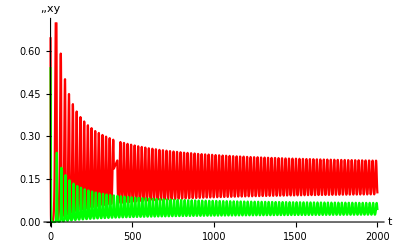

Fig5T.pdf

```mathematica
λ=0.36;β=0.11;δ=0.44;b=28;K=1;γ=1;T1=4000;T2=2000;T=800;
X0={x->0.5,y->0.5,v->1.5};
fpN=fpT(*Numerical values of FP*)
Print["Eigenvalues corresponding to E* are:"]
EcoEigenvalues[fpN[[3]]](*Eigenvalues corresponding to E_*  **)
solE3=EcoSim[RuleListAdd[(fpN[[3]]),X0],T2];

Fig5T=PlotDynamics[{solE3[[1]],solE3[[2]]},PlotRange->{{0,T2},{0,0.7}}]
Export["Fig5T.pdf",Fig5T]
```

```mathematica
E2n=RuleListTweak[fpT[[3]],{x,y},{0.1,0.1}]
Print["Time plot around E2"]
sol=EcoSim[E2n,T2];
lc=FindEcoCycle[FinalSlice[sol]];
cy3D=RuleListPlot[lc,{x,y,v},PlotStyle->Blue];
cy113D=Show[{cy3D,cyR3}]
Export["cy113D.pdf",cy113D]
```

{v→2.64672,x→0.248148,y→0.143132}

Time plot around E2

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

-Graphics3D-

cy113D.pdf

### 1) Numerical simulations:

Bifurcation Diagram:

b0=5.

{{b→-0.347032},{b→0.63211-0.406197 ⅈ},{b→0.63211+0.406197 ⅈ},{b→27.7664}}

bH=27.7664

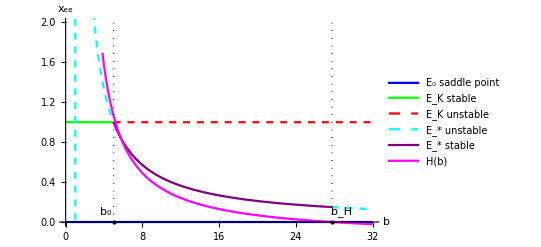

pHb.pdf

bif11T.pdf

```mathematica
Clear["b"];
bL=32;
Print["b0=",bs1//N]
cb=NSolve[(ϕb)==0,b,WorkingPrecision->10]
bM=Max[Table[Re[b/.cb[[i]]],{i,Length[cb]}]];
Print["bH=",bH=N[bM,30]]
fpT//N;
linb0=Line[{{ bs1,0},{ bs1,10}}];
lib0=Graphics[{Thick,Black,Dotted,linb0}];
linbH=Line[{{ bH,0},{ bH,10}}];
libH=Graphics[{Thick,Black,Dotted,linbH}];
px0=Plot[0,{b,0,bL},PlotStyle->{Blue},PlotRange->All,PlotLegends->{"E_0 saddle point"}];
px1a=Plot[{1},{b,0,bs1},PlotStyle->{Green},PlotRange->All,PlotLegends->{"E_K stable"}];
px1b=Plot[1,{b,bs1,bL},PlotStyle->{Red,Dashed},PlotRange->All,
PlotLegends->{"E_K unstable"}];
pxe1=Plot[{x/.fpT[[3]]},{b,0, bs1},PlotStyle->{Cyan,Dashed},PlotRange->All,
PlotLegends->{"E_* unstable"}];
pxe2=Plot[{x/.fpT[[3]]},{b,bs1, bH},PlotStyle->{Purple},PlotRange->All,
PlotLegends->{"E_* stable"}];
pxe2a=Plot[{x/.fpT[[3]]},{b,bH, bL},PlotStyle->{Cyan,Dashed},PlotRange->All];
epi={Text["b_0",Offset[{-8,10},{ bs1,0}]],
{PointSize[Large],Style[Point[{ bs1,0}],Black]},Text["b_H",Offset[{10,10},{ bH,0}]],
{PointSize[Large],Style[Point[{ bH,0}],Black]}};
pHb=Plot[{H2},{b,0,bL},PlotStyle->{Magenta},Epilog->epi,AxesLabel->{"b","H(b)"},PlotLegends->{"H(b)"}];
bif11T=Show[{px0,px1a,px1b,pxe1,pxe2,pxe2a,pHb,lib0,libH},Epilog->epi,
PlotRange->{{0,bL},{0,2}},AxesLabel->{"b","x_ee"}]
pHbS=Show[{pHb,lib0}];
Export["pHb.pdf",pHbS]
Export["bif11T.pdf",bif11T]
```

Time plot when b=28:

{v→2.64672,x→0.348148,y→0.0531317}

Time plot around E2

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],v→InterpolatingFunction[…]}

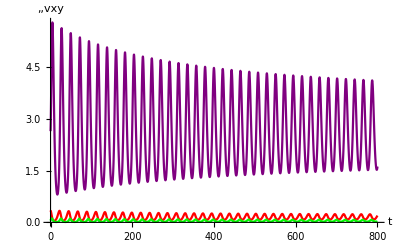

Finding the cycle using time slice

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

{v→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…]}

Final time slice is

21.1984

{{x→0,y→0},{x→1,y→0},{x→0.148148,y→0.0431317}}

FP=

{{x→0,y→0,v→0},{x→1,y→0,v→0},{x→0.148148,y→0.0431317,v→2.64672}}

Eigenvalues of FP:{{-1.,-0.44,0.36},{-2.54436,0.994357,-0.36},{-1.51022,0.000296187+0.298909 ⅈ,0.000296187-0.298909 ⅈ}}

```mathematica
xm=0;ym=0;xM=1;yM=1;b=28;
E2n=RuleListTweak[fpT[[3]],{x,y},{0.2,0.01}]
Print["Time plot around E2"]
sol=EcoSim[E2n,T]
psol=PlotDynamics[sol]
Print["Finding the cycle using time slice"]
lc=FindEcoCycle[FinalSlice[sol]]
Print["Final time slice is"]
FinalTime[lc]

eq={Drop[fpT[[1]],{3}],Drop[fpT[[2]],{3}],Drop[fpT[[3]],{3}]}
Print["FP="]
fpT
Print["Eigenvalues of FP:",EcoEigenvalues[fpT]]
pp=Show[PlotEcoPhasePlane[{x,xm,xM},{y,ym,yM},PlotPoints->180],RuleListPlot[eq,PlotMarkers->EcoStableQ[fpT]]];
(*sp11=Show[pp,RuleListPlot[Drop[sol,{3}],PlotStyle->Blue]]
Export["sp11.pdf",sp11]*)
(*RuleListPlot[Append[eq,lc]]*)
cy1B=RuleListPlot[Drop[sol,{3}],PlotStyle->Blue];
```

{v→2.64672,x→0.248148,y→0.0531317}

FindEcoCycle::cvmit: Failed to converge to the requested accuracy within 100 iterations.

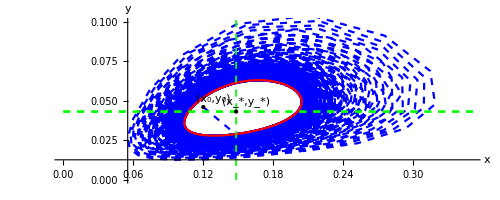

cy11E.pdf

```mathematica
T=3000;
E2nb=RuleListTweak[fpT[[3]],{x,y},{0.1,0.01}]
solb=EcoSim[E2nb,T];
lcb=FindEcoCycle[FinalSlice[solb]];
lcbp=RuleListPlot[lcb,{x,y},PlotStyle->{Black}];
cy1B=RuleListPlot[Drop[solb,{3}],PlotStyle->{Dashed,Blue}];
cy11E=Show[{cyBall,RuleListPlot[lc,{x,y},PlotStyle->{Red}],pyn, Graphics[{Green,Dashed,
Line[{{x/.x->fp[[3,1]],0},{x/.x->fp[[3,1]],1}}]}]},PlotRange->{{0,0.35},{0,0.1}},Epilog->{Text["(x_*,y_*)",
Offset[{10,10},{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}]],
{PointSize[Large],Style[Point[{(x/.x->fp[[3,1]]),(y/.y->fp[[3,2]])}],Black]},{PointSize[Large],Point[{x0n,y0n}]},Text["(x_0,y_0)",Offset[{10,8},{x0n,y0n}]]}]
(*cy11F=Show[{cy11,RuleListPlot[lc,{x,y},PlotStyle->{Red}]}]*)

Export["cy11E.pdf",cy11E]
(*Export["cy11F.pdf",cy11F]*)
```

#### Linear birth model

```mathematica
x1=λ x-   β x v ;
y1=β x v - γ y;
v1=-β x v + b  γ y - δ v;
dyn={x1,y1,v1}/.βy->0/.βv->0(*Tian 11 case with K>0*)
dynKeq1=dyn/.c3dim;

cfp=Solve[Thread[dyn=={0,0,0}],{x,y,v}]//FullSimplify;
fp=X/.cfp

Print["Number of fixed points is ",Length[fp]," The ee FP is E*="]
fp[[2]]//FullSimplify
fpN=fp/.c3dim/.parN;

(*"Jacobian is"*)
Jac=Grad[dyn,{x,y,v}]//FullSimplify;
Jst=Jac/.cfp[[2]];
Print["J(E_*)= ",Jst//MatrixForm," det= ",Det[Jst]//Factor]



(*Routh Hurwitz conditions for the stability of E_***)
pc=Collect[Det[ψ IdentityMatrix[3]-Jst],ψ];
coT=CoefficientList[pc,ψ]//FullSimplify;
Print["a_1=",a1=Apart[coT[[3]]]//.c3dim, ", a_2=",a2=coT[[2]]//.c3dim, ", a_3=",a3=coT[[1]]//.c3dim]
H2=a1*a2-a3;
Print["Hurw(b) when K=γ=1 is H2=", H2//.c3dim//FullSimplify]
Print["H2(b0) when K=γ=1 is",H2/.b->b0//.c3dim//FullSimplify]
Print["Denominator of H2 is posi",Denominator[Together[H2]]/.K->1//FullSimplify]
Together[H2//FullSimplify];
ϕb=Collect[Numerator[Together[H2]]/(δ λ),b]/.K->1//FullSimplify;
Print["ϕ(b)=", Collect[ϕb,b]]
cofi=CoefficientList[ϕb,b]//FullSimplify;
Print["Coefficients of numerator ϕ(b)are {B0,B1,B2}=",cofi]
bH=Solve[ϕb==0,b][[2]]
```

{-v x β+x λ,v x β-y γ,-v x β+b y γ-v δ}

{{0,0,0},{δ/((-1+b) β),(δ λ)/((-1+b) β γ),λ/β}}

Number of fixed points is 2 The ee FP is E*=

{δ/((-1+b) β),(δ λ)/((-1+b) β γ),λ/β}

J(E_*)= (0 | 0 | -δ/(-1+b)
λ | -γ | δ/(-1+b)
-λ | b γ | -δ-δ/(-1+b)) det= -γ δ λ

a_1=1+(b δ)/(-1+b), a_2=(δ λ)/(1-b), a_3=δ λ

Hurw(b) when K=γ=1 is H2=-(b δ (-1+b+δ) λ)/(-1+b)^2

H2(b0) when K=γ=1 is-((1+β) (β+δ) λ)

Denominator of H2 is posi(-1+b)^2

ϕ(b)=-b^2-b (-1+δ)

Coefficients of numerator ϕ(b)are {B0,B1,B2}={0,1-δ,-1}

{b→1-δ}